## Load packages

```mathematica
<<"ExtFileLoading.wl";
<<"DegFileNamings.wl";
<<"PlotMatexFormatting.wl";
<<"ArrayManip.wl";
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Ohdraw.niL\OneDrive - UC San Diego\Programming\Julia\practice\Monte_Carlo_Ising

## Read file

```mathematica
fileName="meanSpinLst_it10000_sz16_AB_1Heat_1Metrop.jld2";
```

```mathematica
meanSpinLstAB=readJuliaVar[fileName,"meanSpinLstAB"];
```

```mathematica
meanSpinLst1Heat=readJuliaVar[fileName,"meanSpinLstSingleHeatBath"];
meanSpinLst1Metrop=readJuliaVar[fileName,"meanSpinLstSingleMetropolis"];
```

```mathematica
meanSpinLst1Heat//Dimensions
```

{100000}

```mathematica
Max[meanSpinLst1Heat]
```

0.217285

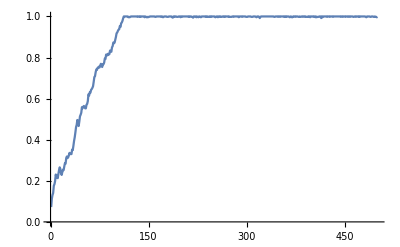

```mathematica
ListLinePlot[meanSpinLstAB⟦1;;500⟧,PlotRange->Full]
```

```mathematica
lineStyleLst=lineStyleLstFunc[colorLst,dataThick];
```

```mathematica
lineStyleLst//Dimensions
```

{101,2}

lineStyleLstFunc[AbsoluteThickness[1]]

```mathematica
axisLabLst=matexLstFunc[{"\\mathrm{it}","\\left| \\langle s \\rangle \\right|"},labMag];
```

```mathematica
axisLabLst
```

{-Graphics-,-Graphics-}

```mathematica
legLabLst=matexLstFunc[{"\\mathrm{checkerboard}","\\mathrm{Metropolis}"},labMag];
```

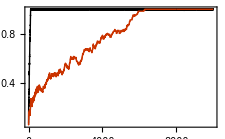

```mathematica
ListLinePlot[{meanSpinLstAB,-meanSpinLst1Metrop⟦1;;10000⟧},PlotRange->Full,ImageSize->8cm,BaseStyle->texStyle,PlotStyle->lineStyleLst,Frame->True,FrameLabel->axisLabLst,PlotRangePadding->{None,{None,Automatic}},PlotLegends->Placed[LineLegend[legLabLst],Scaled[{0.75,0.25}]]]
```